```mathematica
lvsDeltaEPBC={{20,109.323525211403},{24,131.19292695662952},{28,151.68021255173983},{32,173.60464948987908},{36,194.05783181658052},{40,215.9918189618297},{44,234.2859912941605},{48,258.371994594021}}
```

{{20,109.324},{24,131.193},{28,151.68},{32,173.605},{36,194.058},{40,215.992},{44,234.286},{48,258.372}}

```mathematica
lvsDeltaEOBC={{20,50.85349216171575},{24,62.69998750037272},{28,72.12827067923402},{32,84.29582349285805},{36,93.36260570183538},{40,105.53012310873606},{44,114.59866679672383}}
```

{{20,50.8535},{24,62.7},{28,72.1283},{32,84.2958},{36,93.3626},{40,105.53},{44,114.599}}

```mathematica
PBCInverseTable=N[Table[{1/(lvsDeltaEPBC[[i]][[1]]),1/(lvsDeltaEPBC[[i]][[2]])},{i,1,Dimensions[lvsDeltaEPBC][[1]]}]]
```

{{0.05,0.00914716},{0.0416667,0.00762236},{0.0357143,0.00659282},{0.03125,0.00576021},{0.0277778,0.0051531},{0.025,0.0046298},{0.0227273,0.00426829},{0.0208333,0.00387039}}

```mathematica
OBCInverseTable=N[Table[{1/(lvsDeltaEOBC[[i]][[1]]),1/(lvsDeltaEOBC[[i]][[2]])},{i,1,Dimensions[lvsDeltaEOBC][[1]]}]]
```

{{0.05,0.0196643},{0.0416667,0.015949},{0.0357143,0.0138642},{0.03125,0.011863},{0.0277778,0.0107109},{0.025,0.00947597},{0.0227273,0.00872611}}

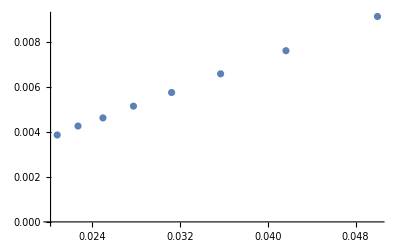

```mathematica
ListPlot[PBCInverseTable]
```

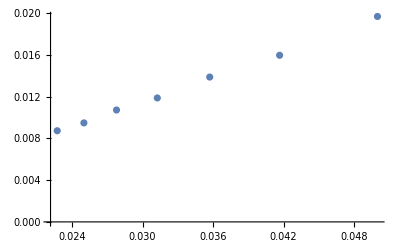

```mathematica
ListPlot[OBCInverseTable]
```

```mathematica
Fit[PBCInverseTable,{1,x},x]
```

0.00014621+0.179921 x

```mathematica
Fit[OBCInverseTable,{1,x},x]
```

-0.000462225+0.399294 x